```mathematica
NewtonRaphson[f_, x0_, max_] := Module[{},
k=0;
p0=N[x0];
p1=p0;
While[k<max,
p0=p1;
p1=p0 - N[f[p0]]/N[f'[p1]];
k++;
];
Return[p1];
]
```

```mathematica
f[x_] := x^3 - 6*x^2+11x-6.1;
```

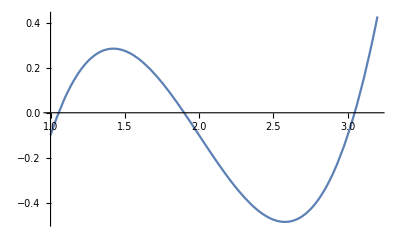

```mathematica
Plot[f[x], {x, 1, 3.2}]
```

```mathematica
NewtonRaphson[f, 3.5, 3]
```

3.04732

```mathematica
SecantMethod[f_, x0_, x1_, max_] := Module[{},
k=1;
p0=N[x0];
p1=N[x1];
p2=p1;
p1=p0;
While[k<max,
p0=p1;
p1=p2;
p2=p1 - (f[p1]*(p1-p0)) / (f[p1]-f[p0]);
k++;
];
Return[p2];
]
```

```mathematica
SecantMethod[f, 3.5, 2.5, 3]
```

6.77026

```mathematica
SecantMethodErr[f_, x0_, x1_, delta_] := Module[{},
k=1;
p0=N[x0];
p1=N[x1];
deltap=1;
While[And[delta<Abs[deltap]],
deltap = (f[p1]*(p1-p0)) / (f[p1]-f[p0]);
p2=p1-deltap;
k++;
p0=p1;
p1=p2;
];
Return[p2];
]
```

```mathematica
SecantMethodErr[f, 3.5, 2.5, 0.001]
```

3.04668

```mathematica
Roots[f[x]==0, x]
```

x==1.05435||x==1.89897||x==3.04668